# Michaelmas term

```mathematica
(*Get a fresh mind*)
Quit[]
```

```mathematica
(*Relativity Sheet 1*)
ClearAll["Global`*"]
Simplify[D[(Cos[θ]-v)/(1-v*Cos[θ]),θ]]//TraditionalForm
```

((v^2-1) sin(θ))/(v cos(θ)-1)^2

```mathematica
(*Relativity Sheet 1*)
ClearAll["Global`*"]
c=299792458.;
g=9.8;
target=10*365*c*24*3600;  (*10 light-years in meters*)

sol=Solve[(c^2/g)*(Cosh[g*t/c]-1)==target && t>0,t];
τ=sol[[1,All,2]];

(*time in the original frame in years*)
(c/g)*Sinh[g*τ/c]/(3600*24*365)

(*proper time in years*)
τ /(3600*24*365)
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{10.9271}

{3.02339}

```mathematica
(*Relativity Sheet 1*)
m=Entity["Element","Hydrogen"]["AtomicMass"]//UnitConvert[#,"Kilograms"] &;
moleculeMass = 2*m;
k=Quantity[0.025,"Electronvolts"]//UnitConvert[#,"Joules"]&;
c=Quantity["SpeedOfLight"];

vclassic=Sqrt[2*k/moleculeMass];

gamma[v_]:=1/Sqrt[1-(v/c)^2];
relKE[v_]:=(gamma[v]-1)*moleculeMass*c^2;

sol=Solve[{relKE[v]==k,v>0},v][[1,All,2]];

(*Time to travel 20 mm*)
t = (Quantity[20, "Millimeters"]/sol);
t//ScientificForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{1.29288×10^-5 s}

```mathematica
(*Relativity Sheet 1*)m=Entity["Particle","Muon"]["Mass"]//UnitConvert[#,"Kilograms"] &;
moleculeMass = m;
k=Quantity[3.1,"GigaElectronvolts"]//UnitConvert[#,"Joules"]&;
c=Quantity["SpeedOfLight"];

gamma[v_]:=1/Sqrt[1-(v/c)^2];
relKE[v_]:=(gamma[v]-1)*moleculeMass*c^2;

sol=Solve[{relKE[v]==k,v>0},v][[1,All,2]];
gamma[sol]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{30.3398}

```mathematica
Series[Log[1+Exp[β(x-µ)]],{x,0,3}]//TraditionalForm
```

log(ⅇ^(-β µ)+1)+(β x)/(ⅇ^(β µ)+1)+(β^2 x^2 ⅇ^(β µ))/(2 (ⅇ^(β µ)+1)^2)+(β^3 x^3 ⅇ^(β µ) (ⅇ^(β µ)-1))/(6 (ⅇ^(β µ)+1)^3)+O(x^4)

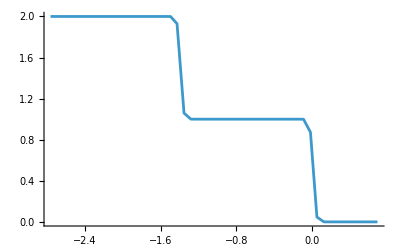

```mathematica
(*Statistical Mechanics Q11*)
ClearAll["Global`*"];
kb=Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
T=Quantity[1,"Kelvins"];
β=1/(kb*T);
U=100/β;
Plot[2*(Exp[-β*x]+Exp[-β*(2*x + U)])/(1+2*Exp[-β*x]+Exp[-β*(2*x + U)]),{x,-2*U,0.5*U}]
```

```mathematica
(*Factor for helium ionisation question*)
ClearAll["Global`*"];
kb=Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
T=Quantity[1*^4,"Kelvins"];
β=1/(kb*T);
ϕ=Quantity[-24.6,"Electronvolts"]//UnitConvert[#,"Joules"]&;
(*p=Quantity[1,"Atmospheres"]//UnitConvert[#,"Kilograms"/("Meters"*"Seconds"^2)]&;*)
p=Quantity[1*^-2,"Kilograms"/("Meters"*"Seconds"^2)];
hbar=Entity["PhysicalConstant","PlanckConstant"]["Value"]/(2*Pi);
m=Entity["Particle","Electron"]["Mass"]//UnitConvert[#,"Kilograms"] &;
ratio=(kb*T/p)*((m*kb*T/(2*Pi*hbar^2))^(3/2))*Exp[β*ϕ]
Solve[x^2==(1+2*x)*ratio,x]//ScientificForm
```

0.0133379

{{x→-1.0292×10^-1},{x→1.29596×10^-1}}

```mathematica
(*Q13 E&O sheet*)
ClearAll["Global`*"];
λ=Quantity[656,"Nanometers"]//UnitConvert[#,"Meters"] &;
dl=Quantity[2,"Millimeters"]//UnitConvert[#,"Meters"] &;
c=Quantity[299792458,"Meters"/"Seconds"];
lc=Quantity[5,"Millimeters"]//UnitConvert[#,"Meters"] &;
m=Entity["Particle","Proton"]["Mass"]//UnitConvert[#,"Kilograms"] &;
kb=Entity["PhysicalConstant","BoltzmannConstant"]["Value"]//UnitConvert[#,"Kilograms"*"Meters"^2/("Seconds"^2*"Kelvins")] &;
(*N[λ*c/(4*dl)]*)
dlam=λ^2/(2*lc);
T=(dlam^2*m*c^2)/(kb*λ^2)
```

46855.82443 K

```mathematica
(*Q14 E&O sheet*)
ClearAll["Global`*"];
λ=Quantity[643.847,"Nanometers"]//UnitConvert[#,"Meters"] &;
dlam=Quantity[0.0013,"Nanometers"]//UnitConvert[#,"Meters"] &;
lc=λ^2/(2*dlam)
```

0.159438 m

```mathematica
(*Q12、13 AQP*)
ClearAll["Global`*"];
Integrate[r^2*((1/r)-(1/b))*(1-(r/(2*a)))^2,{r,0,b}]
Series[Integrate[r^4*((1/r)-(1/b))*Exp[-r/a],{r,0,b}]*2/3,{b,0,6}]
Series[Integrate[r^4*((1/r)-(1/b))*Exp[-r/a],{r,0,b}]*Integrate[Sin[x]^3,{x,0,Pi}],{b,0,6}]
Integrate[r^4*Exp[-2*r/a],{r,0,Infinity}]*Integrate[Cos[x]^2*Sin[x],{x,0,Pi}]
```

b^2/6-b^3/(12 a)+b^4/(80 a^2)

b^4/30-b^5/(45 a)+b^6/(126 a^2)+O[b]^7

b^4/15-(2 b^5)/(45 a)+b^6/(63 a^2)+O[b]^7

ConditionalExpression[a^5/2, Re[a]>0]

```mathematica
Sqrt[Integrate[(a^2-x^2)^2,{x,-a,a}]];
A^2*Integrate[(a^2-x^2)*((hbar^2/m)+(m*ω^2*(a^2*x^2-x^4))/2),{x,-a,a}]
N[(5/2)*Sqrt[2/35]]
```

A^2 ((4 a^3 hbar^2)/(3 m)+8/105 a^7 m ω^2)

0.597614

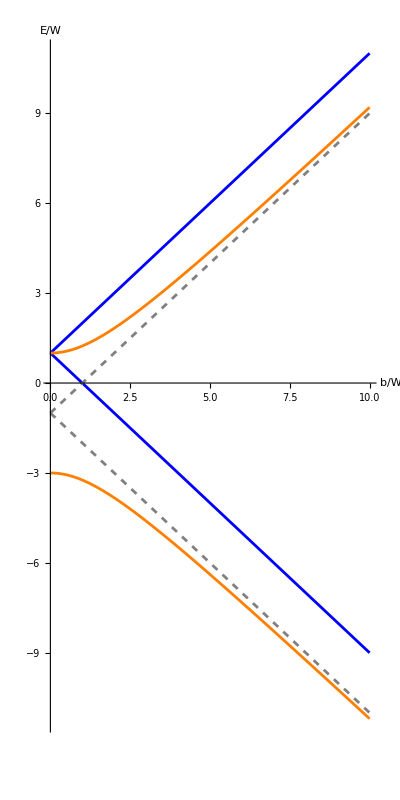

```mathematica
(*Q17 AQP sheet*)
Clear[x]
pic1=Plot[x+1,{x,0,10},PlotStyle->{Blue}];
pic2=Plot[-x+1,{x,0,10},PlotStyle->{Blue}];
pic3=Plot[-1+Sqrt[4+x^2],{x,0,10},PlotStyle->{Orange}];
pic4=Plot[-1-Sqrt[4+x^2],{x,0,10},PlotStyle->{Orange}];
pic5=Plot[x-1,{x,0,10},PlotStyle->{Gray,Dashed}];
pic6=Plot[-x-1,{x,0,10},PlotStyle->{Gray,Dashed}];
Show[pic1,pic2,pic3,pic4,pic5,pic6,{PlotRange->All,AspectRatio->2,AxesLabel->{"b/W","E/W"}}]
```

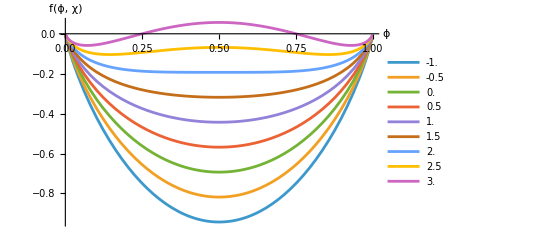

```mathematica
(*Binary mixture*)
Clear[χ,ϕ]
f[ϕ_,χ_]:=ϕ*Log[ϕ]+(1-ϕ)*Log[1-ϕ]+χ*ϕ*(1-ϕ);
Plot[Evaluate@Table[f[ϕ,χ],{χ,-1,3,0.5}],{ϕ,0.001,0.999},PlotLegends->Table[χ,{χ,-1,3,0.5}],PlotRange->All,AxesLabel->{"ϕ","f(ϕ, χ)"}]
```

```mathematica
(*Binary mixture and first order phase transitions - Solve T^* *)
ClearAll["Global`*"];
Solve[{a*(t-tc)-b*ρ+c*ρ^2==0,2*a*(t-tc)-3*b*ρ+4*c*ρ^2==0},{ρ,t}]
```

{{ρ→0,t→tc},{ρ→b/(2 c),t→(b^2+4 a c tc)/(4 a c)}}

```mathematica
(*Calculate thermal De Broglie wavelength*)
ClearAll["Global`*"];
kb=Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
T=Quantity[1.6*^7,"Kelvins"];
hbar=Entity["PhysicalConstant","PlanckConstant"]["Value"]/(2*Pi);
me=Entity["Particle","Electron"]["Mass"]//UnitConvert[#,"Kilograms"] &;
mp=Entity["Particle","Proton"]["Mass"]//UnitConvert[#,"Kilograms"] &;
mn=Entity["Particle","Neutron"]["Mass"]//UnitConvert[#,"Kilograms"] &;
c=Quantity[299792458,"Meters"/"Seconds"];
m=2*mp+2*mn;
Wavelength[m_]:=Sqrt[2*Pi*hbar^2/(m*kb*T)]//UnitConvert[#,"Meters"] &;
DensityLimit[m_]:=m/Wavelength[m]^3;
NDensity[ρ_,m_]:=ρ/m;
<<PhysicalConstants`;
StefanConstant;
σ=UnitConvert[Quantity["StefanBoltzmannConstant"],"SIBase"];
(NDensity[46.28,me]+NDensity[6*^4,mp]+NDensity[1*^5,(2*mp+2*mn)])*kb*T
4*σ*T^4/(3* c)
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

2.24467×10^16 J/kg

1.65276×10^13 kg/(m s^2)

```mathematica
(*He-3 superflow, effective mass enhanced by 2.4*)
ClearAll["Global`*"];
kb=Entity["PhysicalConstant","BoltzmannConstant"]["Value"];
hbar=Entity["PhysicalConstant","PlanckConstant"]["Value"]/(2*Pi);
mp=Entity["Particle","Proton"]["Mass"]//UnitConvert[#,"Kilograms"] &;
mn=Entity["Particle","Neutron"]["Mass"]//UnitConvert[#,"Kilograms"] &;
m4=2*mp+2*mn;
m3=2*mp+mn;
n=Solve[n*m3+19*n*m4==140,n][[1,All,2]];
tf=hbar^2*(3*Pi^2*n)^(2/3)/(2*2.4*m3*kb) (*ignore units*)
γ=Pi^2*kb/(2*tf)(*ignore units*)
```

{0.33235 s^2 K J/kg^(5/3)}

{2.05002×10^-22 kg^(5/3)/(s^2 K^2)}

```mathematica
(*O&E pulsar question*)
ClearAll["Global`*"];
μ=Entity["PhysicalConstant","MagneticConstant"]["Value"];
c=Quantity[299792458,"Meters"/"Seconds"];
t=Quantity[33*^-3,"Seconds"];
ω=2*Pi/t;
dt=Quantity[36*^-9,"Seconds"/"Days"]//UnitConvert[#,"Seconds"/"Seconds"]&;
do=-2*Pi*dt/t^2;
ddt=-3*dt^2/t;
r=Quantity[7000,"Meters"];
m=Quantity[2*^30,"Kilograms"];
energy=m*ω^2*r^2/5;
power=2*m*ω*r^2*do/5;
redpower=μ*ω^4/(6*Pi*c^3);
moment=Sqrt[-power/redpower]//UnitConvert[#] &;
N[redpower]
```

3.2517×10^-24 H/(m^4 s)

```mathematica
(*Polarisation of sky in Cambridge*)
ClearAll["Global`*"];
angle=52*Pi/180;
cossquared=Cos[angle]^2;
polarisation=(1-cossquared)/(1+cossquared);
N[polarisation]
```

0.450285

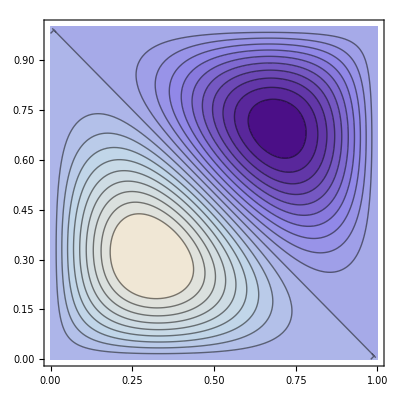

```mathematica
(*Identical particles question in AQP*)
ClearAll["Global`*"];
L=1;
(*Wavefunctions*)
symmetric[x1_,x2_,L_]:=Sin[Pi*x1/L]*Sin[2*Pi*x2/L]+Sin[2*Pi*x1/L]*Sin[Pi*x2/L];
antisymmetric[x1_,x2_,L_]:=Sin[Pi*x1/L]*Sin[2*Pi*x2/L]-Sin[2*Pi*x1/L]*Sin[Pi*x2/L];
ContourPlot[symmetric[x1,x2,L],{x1,0,L},{x2,0,L},Contours->20,ColorFunction->"LakeColors",PlotPoints->50]
(*If you want 3D plots, use the following*)(*Plot3D[symmetric[x1,x2,L],{x1,0,L},{x2,0,L},PlotRange->All,AxesLabel->{"x1","x2","f"},ColorFunction->"LakeColors",Mesh->None]*)
(*If you want to plot wavefunction squared, use the following*)
(*ContourPlot[antisymmetric[x1,x2,L]^2,{x1,0,L},{x2,0,L},Contours->10,ColorFunction->"LakeColors",PlotPoints->50]*)
```

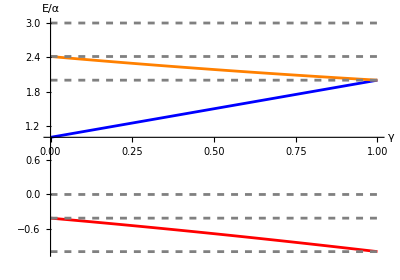

```mathematica
(*He3+ ground state from LCAO*)
ClearAll["Global`*"];
α=1;
β=-1;
e1[γ_]:=(α-γ*β)/α;
e2[γ_]:=(α+(1/2)*β*(γ+Sqrt[γ^2+8]))/α;
e3[γ_]:=(α+(1/2)*β*(γ-Sqrt[γ^2+8]))/α;
pic1=Plot[e1[x],{x,0,1},PlotStyle->{Blue}];
pic2=Plot[e2[x],{x,0,1},PlotStyle->{Red}];
pic3=Plot[e3[x],{x,0,1},PlotStyle->{Orange}];
pic4=Plot[(α-Sqrt[2]*β)/α,{x,0,1},PlotStyle->{Gray,Dashed}];
pic5=Plot[(α-β)/α,{x,0,1},PlotStyle->{Gray,Dashed}];
pic6=Plot[(α-2*β)/α,{x,0,1},PlotStyle->{Gray,Dashed}];
pic7=Plot[(α+β)/α,{x,0,1},PlotStyle->{Gray,Dashed}];
pic8=Plot[(α+2*β)/α,{x,0,1},PlotStyle->{Gray,Dashed}];
pic9=Plot[(α+Sqrt[2]*β)/α,{x,0,1},PlotStyle->{Gray,Dashed}];
Show[pic1,pic2,pic3,pic4,pic5,pic6,pic7,pic8,pic9,{PlotRange->All,AspectRatio->0.7,AxesLabel->{"γ","E/α"}}]
```